```mathematica
(* 1.Define Golden ratio .show that the value of golden ratio is the root of the equation x^2-x-1=0 *)
```

```mathematica
x=GoldenRatio;
N[x^2-x-1]
```

0.

```mathematica
(* 2. Find the greatest common divisor (GCD) & least common multiple (LCM) 0f 1001 and 1331  *)
```

```mathematica
GCD[1001,1331]
```

11

```mathematica
LCM[1001,1331]
```

121121

```mathematica
(* 3. Define the piecewise function f(x) as a mathematica function & sketch the graph from x= -4 to 4 *)
```

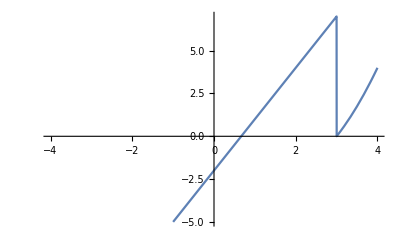

```mathematica
f[x_]:=3*x-2/;-1<x≤3
f[x_]:=x^2-3*x/;3<x<4
f[x_]:=3*x+1/;x≥4
Plot[f[x],{x,-4,4}]
```

```mathematica
(* Find the sum of the following series:

    (i)1/(3.4.5)+1/(4.5.6)+1/(5.6.7)+...upto n
(ii)4/(1.2.3)+5/(2.3.4)+6/(3.4.5)+...upto ∞  *)
```

```mathematica
Sum[1/((4i+1)(4i+5)(4i+9)),{i,1,n}]
```

(7 n+2 n^2)/(45 (5+4 n) (9+4 n))

```mathematica
Sum[(i+3)/(i(i+1)(i+2)),{i,1,∞}]
```

5/4

```mathematica
(* 5. Using do loop, for loop ,while loop write down the mathematical command to compute the value of 13!  *)
```

```mathematica
fact=1;
n=13;
Do[fact=fact*k,{k,n}]
fact
```

6227020800

```mathematica
fact=1;
n=13;
While[n>0,fact=fact*n;n--]
fact
```

6227020800

```mathematica
For[fact=1;n=1,n≤13,n++,fact=n*fact]
fact
```

6227020800